```mathematica
y^2==x(x^2+109*x+224)
```

```mathematica
sol=Solve[{y^2==x(x^2+109*x+224),y>0,x!=0},{x,y},Integers];
DeleteCases[{x,y}/.sol,{x,ConditionalExpression[_,_]}]
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{{-100,260},{-56,392},{-9,78},{-4,28}}

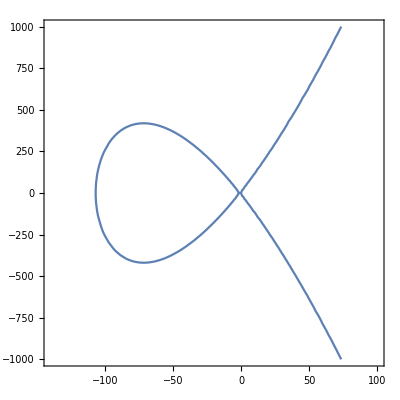

```mathematica
ContourPlot[y^2==x(x^2+109*x+224),{x,-140,100},{y,-1000,1000}]
```

```mathematica
ecr=ImplicitRegion[y^2==x (x-1) (x+1),{{x,-2,2},{y,-2,2}}];
BlockRandom[SeedRandom["elliptic"];(*for reproducibility*)(*Quiet suppresses a few harmless error messages*){p1,p2}=Quiet[RandomPoint[ecr,2]];]
```

```mathematica
n==a/(b+c)+b/(c+a)+c/(a+b)
```

n==c/(a+b)+b/(a+c)+a/(b+c)

```mathematica
Clear[n]
```

```mathematica
n=2
(*FindInstance[n==c/(a+b)+b/(a+c)+a/(b+c),{a,b,c},Integers]*)
A=4n^2+12n-3;B=32(n+3);
Solve[{y^2==x(x^2+A x+B),y>0,x!=0},{x,y},Integers]
DeleteCases[{x,y}/.sol,{x,ConditionalExpression[_,_]}]
y^2==x(x^2+A x+B)
```

2

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{{y→ConditionalExpression[√(160 x+37 x^2+x^3),(x|√(160 x+37 x^2+x^3))∈ℤ&&x≥1]},{x→-20,y→60},{x→-8,y→24}}

{{-200,680},{-81,918},{-36,468},{-8,104}}

y^2==x (160+37 x+x^2)

```mathematica
x==-4(a+b+2c)(n+3)/((2+n) a+(1+n)b-c)//FullSimplify
y==4(a-b)(2 n^2+11n+15)/((2+n) a+(1+n)b-c)//FullSimplify
```

x==-(20 (a+b+2 c))/(4 a+3 b-c)

y==(180 (a-b))/(4 a+3 b-c)

```mathematica
ECplus[p1_,p2_]:=Block[
{a,b,k,x3,x1,y1,x2,y2},
{a,b}=para;{x1,y1}=p1;{x2,y2}=p2;
If[p1!=p2,k=(y1-y2)/(x1-x2),k=(3x1^2+a)/(2y1)];
{x3=k^2-x1-x2,-(y1+k(x3-x1))}
]
ECplusN[p1,p2]
ECplus[p1,p2]
```

{353.44,-7605.73}

{960631881/270400,-29774370745029/140608000}

```mathematica
Arrow[nl]
```

Arrow[{{-100,260},{353.44,-7605.73},{-61.5289,407.35},{67.1989,-900.396},{-28.0324,239.471},{19.1137,-226.022},{-11.4647,101.252},{5.67977,-70.5111},{-4.89865,37.4273},{1.376,-22.7422},{-2.59723,11.6607},{0.0977549,-4.78953},{-2.10009,-1.02445}}]

```mathematica
ECplus[p1_,p2_]:=Block[
{A,B,k,x,y,x1,y1,x2,y2},
{A,B}=para;{x1,y1}=p1;{x2,y2}=p2;
{x,-y}/.If[p1==p2,
Solve[{
y^2==x(x^2+A x+B),
(y-y1)/(x-x1)==(3x1^2+2 A x1+B)/(2y1)
},{x,y}]//First,
Solve[{
y^2==x(x^2+A x+B),
(y-y1)/(x-x1)==(y1+y2)/(x1-x2),
x≠x1,x≠x2
},{x,y}]//First
]
]

(*ECtimes[p1_,n_Integer]*)
```

```mathematica
n=38


para={A,B}={4n^2+12n-3,32(n+3)};
sol=Solve[{Echo[y^2==x(x^2+A x+B),"Ec: "],y>0,x!=0},{x,y},Integers];
ji=DeleteCases[{x,y}/.sol,{x,ConditionalExpression[_,_]}]
iv=Interval[
{(3-12n-4n^2)/2-(2n+5)Sqrt[4n^2+4n-15]/2,-2(n+3)(n+Sqrt[n^2-4])},
{-2(n+3)(n-Sqrt[n^2-4]),-4(n+3)/(n+2)}
]//N
sp=RandomChoice@ji
ECplusN[p1_,p2_]:=Re@N@EllipticExp[EllipticLog[p1,para]+EllipticLog[p2,para],para]
nl=NestWhileList[ECplusN[sp,#]&,sp,!IntervalMemberQ[iv,First@#]&]
ECplus[p1_,p2_]:=Block[
{A,B,k,x,y,x1,y1,x2,y2},
{A,B}=para;{x1,y1}=p1;{x2,y2}=p2;
{x,-y}/.If[p1==p2,
Solve[{
y^2==x(x^2+A x+B),
(y-y1)/(x-x1)==(3x1^2+2 A x1+B)/(2y1)
},{x,y}]//First,
Solve[{
y^2==x(x^2+A x+B),
(y-y1)/(x-x1)==(y1-y2)/(x1-x2),
x≠x1,x≠x2
},{x,y}]//First
]
]
eci=Rule@@@Transpose[{{x,y},Nest[ECplus[sp,#]&,sp,Length@nl-1]}]
fii=Solve[{
a/(a+b+c)==(8n+24-x+y)/(24+8 n-6 x-2 n x),
b/(a+b+c)==(8n+24-x-y)/(24+8 n-6 x-2 n x),
c/(a+b+c)==(4 n+12+2 x+n x)/(3 x+n x-4 n-12),
a>=b>=c>0
}/.eci,{a,b,c},Integers];
finally=fii/.{ConditionalExpression[x_,_]->First@x}//First
c/(a+b)+b/(a+c)+a/(b+c)/.finally
```

8

Ec:  y^2==x (352+349 x+x^2)

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{}

Interval[{-347.988,-346.411},{-5.58873,-4.4}]

RandomChoice::lrwl: 选项 {} 应该是一个列表或者一个规则 weights -> choices.

RandomChoice[{}]

{RandomChoice[{}]}

Transpose::nmtx: {{x,y},RandomChoice[{}]} 的前两层无法转置.

Transpose[{x,y}→RandomChoice[{}]]

ReplaceAll::reps: {Transpose[{x,y}→RandomChoice[{}]]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Solve::naqs: {a/(a+b+c)==(88-x+y)/(88-22 x),b/(a+b+c)==(88-x-y)/(88-22 x),c/(a+b+c)==(44+10 x)/(-44+11 x),a≥b≥c>0}/.Transpose[{x,y}→RandomChoice[{}]] 不是由方程和不等式组成的一个量化系统.

First::normal: First[x] 中的位置 1 处应该是非原子表达式.

{a/(a+b+c)==(88-x+y)/(88-22 x),b/(a+b+c)==(88-x-y)/(88-22 x),c/(a+b+c)==(44+10 x)/(-44+11 x),a≥b≥c>0}/.Transpose[{x,y}→RandomChoice[{}]]

ReplaceAll::reps: {{a/(a+b+c)==(88-x+y)/(88+Times[«2»]),b/(a+b+c)==(88-x-y)/(88+Times[«2»]),c/(a+b+c)==(44+10 x)/(-44+Times[«2»]),a≥b≥c>0}/.Transpose[{x,y}→RandomChoice[{}]]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

c/(a+b)+b/(a+c)+a/(b+c)/.({a/(a+b+c)==(88-x+y)/(88-22 x),b/(a+b+c)==(88-x-y)/(88-22 x),c/(a+b+c)==(44+10 x)/(-44+11 x),a≥b≥c>0}/.Transpose[{x,y}→RandomChoice[{}]])

```mathematica
c/(a+b)+b/(a+c)+a/(b+c)/.{a->"3",b->"1",c->"1"}
```

3/(2 1)+(2 1)/(1+3)